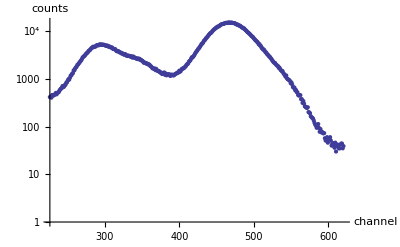

```mathematica
Data = Import["C:\\Users\\Jackson\\Documents\\GitHub\\AdvanceLab\\Gama_Spectroscopy\\data\\Co-57_16xGain.tsv"][[26;;,{2,3}]];
ListLogPlot[Data[[230;;-400]]]
```

{a→13701.7,b→468.689,c→24.4822,d→-7.08584,p→4607.59}

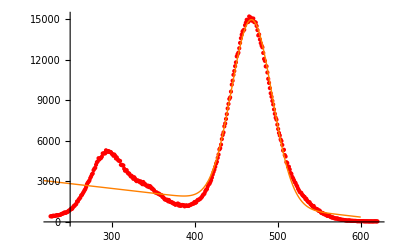

```mathematica
BigPeak=Data[[230;;-400]];
FindFit[BigPeak,a E^(-(x-b)^2/(2 c^2))+d x+p,{{a,12000},{b,500},{c,20},d,p},x]
p1 = Plot[a E^(-(x-b)^2/(2 c^2))+d x+p/.%,{x,200,600},PlotStyle->{Orange,Thick}];
p2 = ListPlot[BigPeak,PlotStyle->{Red}];
Show[p2,p1]
```

{a_1→14335.3,b_1→468.049,c_1→26.5771,a_2→2199.13,b_2→331.1,c_3→18.2384,a_3→3517.18,b_3→291.583,c_2→32.9113,d→-0.59228,p→703.406}

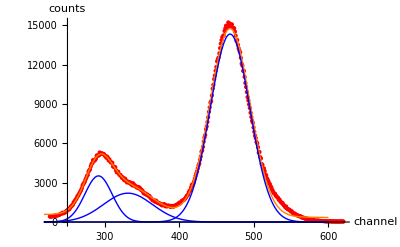

```mathematica
BigPeak=Data[[230;;-400]];
FindFit[BigPeak,Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p,{{Subscript[a, 1],12000},{Subscript[b, 1],500},{Subscript[c, 1],20},{Subscript[a, 2],5000},{Subscript[b, 2],300},{Subscript[c, 3],100},{Subscript[a, 3],5000},{Subscript[b, 3],300},{Subscript[c, 2],100},d,p},x]

p1 = Plot[Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p/.%,{x,200,600},PlotStyle->{Orange}];
FindFit[BigPeak,Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p,{{Subscript[a, 1],12000},{Subscript[b, 1],500},{Subscript[c, 1],20},{Subscript[a, 2],5000},{Subscript[b, 2],300},{Subscript[c, 3],100},{Subscript[a, 3],5000},{Subscript[b, 3],300},{Subscript[c, 2],100},d,p},x];
Do[Subscript[p, i]=Plot[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2))/.%,{x,200,600},PlotStyle->{Blue,Thin},PlotRange->Full],{i,3}]
p2 = ListPlot[BigPeak,PlotStyle->{Red},AxesLabel -> {"channel","counts"}];
Show[p2,p1,Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]]
```

```mathematica
Export["gamaSpeck.png",-Graphics-]
```

gamaSpeck.png